```mathematica
SetDirectory[NotebookDirectory[]];
```

Lattice

### Lattice

#### Area len

```mathematica
squareLength=300;
```

#### Initial

```mathematica
latt=Import["latt_0000.txt","Table"];
lattDict=Association[];
Do[
If[KeyMemberQ[lattDict,l[[3]]],
AppendTo[lattDict[l[[3]]],l[[;;2]]]
,
lattDict[l[[3]]]={l[[;;2]]}
];
,{l,latt}];
```

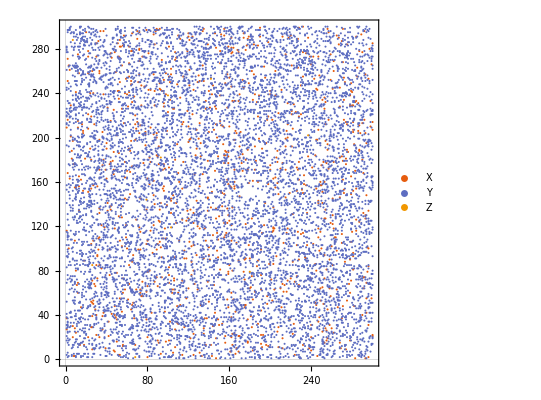

```mathematica
ListPlot[{lattDict["X"],lattDict["Y"],lattDict["Z"]},AspectRatio->1,PlotLegends->{"X","Y","Z"}]
```

```mathematica
visualizeLattice[lattDict,boxLength,{"X","Y","Z"}]
```

-Graphics3D-

#### Second

```mathematica
latt=Import["latt_0100.txt","Table"];
lattDict=Association[];
Do[
lattDict[l[[;;3]]]=l[[4]];
,{l,latt}];
```

```mathematica
visualizeLattice[lattDict,boxLength,{"X","Y","Z"}]
```

-Graphics3D-